```mathematica
<<Notation`;
```

```mathematica
Symbolize[Subscript[u, 1]^t]; Symbolize[Subscript[u, 2]^t]; Symbolize[Subscript[u, 3]^t]; Symbolize[Subscript[u̇, 1]^t]; Symbolize[Subscript[u̇, 2]^t]; Symbolize[Subscript[u̇, 3]^t];Symbolize[Subscript[u^(..), 1]^t]; Symbolize[Subscript[u^(..), 2]^t]; Symbolize[Subscript[u^(..), 3]^t]; Symbolize[Subscript[u, 1]^(t+Δt)]; Symbolize[Subscript[u, 2]^(t+Δt)]; Symbolize[Subscript[u, 3]^(t+Δt)]; Symbolize[Subscript[u̇, 1]^(t+Δt)]; Symbolize[Subscript[u̇, 2]^(t+Δt)]; Symbolize[Subscript[u̇, 3]^(t+Δt)]; Symbolize[Subscript[u^(..), 1]^(t+Δt)]; Symbolize[Subscript[u^(..), 2]^(t+Δt)]; Symbolize[Subscript[u^(..), 3]^(t+Δt)]; Symbolize[Subscript[u, 1]^(t+γΔt)]; Symbolize[Subscript[u, 2]^(t+γΔt)]; Symbolize[Subscript[u, 3]^(t+γΔt)] ; Symbolize[Subscript[u̇, 1]^(t+γΔt)]; Symbolize[Subscript[u̇, 2]^(t+γΔt)]; Symbolize[Subscript[u̇, 3]^(t+γΔt)];Symbolize[Subscript[u^(..), 1]^(t+γΔt)]; Symbolize[Subscript[u^(..), 2]^(t+γΔt)]; Symbolize[Subscript[u^(..), 3]^(t+γΔt)]; Symbolize[Subscript[β, 1]]; Symbolize[Subscript[β, 2]];
```

```mathematica
For[
ClearAll["Global`*"];
γ=1/2;Δt=0.25;Subscript[β, 2]=2 Subscript[β, 1];
Subscript[m, 2]=1;Subscript[m, 3]=1;Subscript[k, 2]=1;ω=1.2;Subscript[u, 1]^(t+Δt)=Sin[ω p];Subscript[u, 1]^(t+γΔt)=Sin[ω (p-Δt/2)];
eq112=Subscript[m, 2] Subscript[u^(..), 2]^(t+γΔt)+(Subscript[k, 1]+Subscript[k, 2]) Subscript[u, 2]^(t+γΔt)+(-Subscript[k, 2]) Subscript[u, 3]^(t+γΔt)==Subscript[k, 1] Subscript[u, 1]^(t+γΔt);
eq113=Subscript[m, 3] Subscript[u^(..), 3]^(t+γΔt)+(-Subscript[k, 2]) Subscript[u, 2]^(t+γΔt)+Subscript[k, 2] Subscript[u, 3]^(t+γΔt)==0;
eq122=Subscript[u, 2]^(t+γΔt)==Subscript[u, 2]^t+(γ Δt)/2(Subscript[u̇, 2]^t+Subscript[u̇, 2]^(t+γΔt));
eq123=Subscript[u, 3]^(t+γΔt)==Subscript[u, 3]^t+(γ Δt)/2(Subscript[u̇, 3]^t+Subscript[u̇, 3]^(t+γΔt));
eq132=Subscript[u̇, 2]^(t+γΔt)==Subscript[u̇, 2]^t+(γ Δt)/2(Subscript[u^(..), 2]^t+Subscript[u^(..), 2]^(t+γΔt));
eq133=Subscript[u̇, 3]^(t+γΔt)==Subscript[u̇, 3]^t+(γ Δt)/2(Subscript[u^(..), 3]^t+Subscript[u^(..), 3]^(t+γΔt));
eq212=Subscript[m, 2] Subscript[u^(..), 2]^(t+Δt)+(Subscript[k, 1]+Subscript[k, 2]) Subscript[u, 2]^(t+Δt)+(-Subscript[k, 2]) Subscript[u, 3]^(t+Δt)==Subscript[k, 1] Subscript[u, 1]^(t+Δt);
eq213=Subscript[m, 3] Subscript[u^(..), 3]^(t+Δt)+(-Subscript[k, 2]) Subscript[u, 2]^(t+Δt)+Subscript[k, 2] Subscript[u, 3]^(t+Δt)==0;
eq222=Subscript[u, 2]^(t+Δt)==Subscript[u, 2]^t+γ Δt((1-Subscript[β, 1])Subscript[u̇, 2]^t+Subscript[β, 1] Subscript[u̇, 2]^(t+γΔt))+(1-γ)Δt((1-Subscript[β, 2])Subscript[u̇, 2]^(t+γΔt)+Subscript[β, 2] Subscript[u̇, 2]^(t+Δt));
eq223=Subscript[u, 3]^(t+Δt)==Subscript[u, 3]^t+γ Δt((1-Subscript[β, 1])Subscript[u̇, 3]^t+Subscript[β, 1] Subscript[u̇, 3]^(t+γΔt))+(1-γ)Δt((1-Subscript[β, 2])Subscript[u̇, 3]^(t+γΔt)+Subscript[β, 2] Subscript[u̇, 3]^(t+Δt));
eq232=Subscript[u̇, 2]^(t+Δt)==Subscript[u̇, 2]^t+γ Δt((1-Subscript[β, 1])Subscript[u^(..), 2]^t+Subscript[β, 1] Subscript[u^(..), 2]^(t+γΔt))+(1-γ)Δt((1-Subscript[β, 2])Subscript[u^(..), 2]^(t+γΔt)+Subscript[β, 2] Subscript[u^(..), 2]^(t+Δt));
eq233=Subscript[u̇, 3]^(t+Δt)==Subscript[u̇, 3]^t+γ Δt((1-Subscript[β, 1])Subscript[u^(..), 3]^t+Subscript[β, 1] Subscript[u^(..), 3]^(t+γΔt))+(1-γ)Δt((1-Subscript[β, 2])Subscript[u^(..), 3]^(t+γΔt)+Subscript[β, 2] Subscript[u^(..), 3]^(t+Δt));
s1and2=Solve[eq112 && eq113 && eq122 && eq123 && eq132 && eq133&&eq212 && eq213 && eq222 && eq223 && eq232 && eq233,{Subscript[u^(..), 2]^(t+γΔt),Subscript[u^(..), 3]^(t+γΔt),Subscript[u̇, 2]^(t+γΔt),Subscript[u̇, 3]^(t+γΔt),Subscript[u, 2]^(t+γΔt),Subscript[u, 3]^(t+γΔt),Subscript[u^(..), 2]^(t+Δt),Subscript[u^(..), 3]^(t+Δt),Subscript[u̇, 2]^(t+Δt),Subscript[u̇, 3]^(t+Δt),Subscript[u, 2]^(t+Δt),Subscript[u, 3]^(t+Δt)}];

Subscript[u^(..), 2]^(t+Δt)=Subscript[u^(..), 2]^(t+Δt)/.s1and2[[1,7]];
Subscript[u^(..), 3]^(t+Δt)=Subscript[u^(..), 3]^(t+Δt)/.s1and2[[1,8]];
Subscript[u̇, 2]^(t+Δt)=Subscript[u̇, 2]^(t+Δt)/.s1and2[[1,9]]; 
Subscript[u̇, 3]^(t+Δt)=Subscript[u̇, 3]^(t+Δt)/.s1and2[[1,10]];
Subscript[u, 2]^(t+Δt)=Subscript[u, 2]^(t+Δt)/.s1and2[[1,11]];
Subscript[u, 3]^(t+Δt)=Subscript[u, 3]^(t+Δt)/.s1and2[[1,12]];
Subscript[k, 1]=10^7;Subscript[β, 1]=0.65;
p=0.25;Subscript[u^(..), 2]^t=0;Subscript[u^(..), 3]^t=0;Subscript[u̇, 2]^t=0;Subscript[u̇, 3]^t=0;Subscript[u, 2]^t=0;Subscript[u, 3]^t=0,
p≤30,
p=p+0.25,
Subscript[uk107b0652, p]=Subscript[u, 2]^(t+Δt);Subscript[uk107b0653, p]=Subscript[u, 3]^(t+Δt);Subscript[uk107b065d2, p]=Subscript[u̇, 2]^(t+Δt);Subscript[uk107b065d3, p]=Subscript[u̇, 3]^(t+Δt);Subscript[uk107b065dd2, p]=Subscript[u^(..), 2]^(t+Δt);Subscript[uk107b065dd3, p]=Subscript[u^(..), 3]^(t+Δt);
Subscript[u^(..), 2]^t=Subscript[u^(..), 2]^(t+Δt);Subscript[u^(..), 3]^t=Subscript[u^(..), 3]^(t+Δt);Subscript[u̇, 2]^t=Subscript[u̇, 2]^(t+Δt);Subscript[u̇, 3]^t=Subscript[u̇, 3]^(t+Δt);Subscript[u, 2]^t=Subscript[u, 2]^(t+Δt);Subscript[u, 3]^t=Subscript[u, 3]^(t+Δt)
];
```

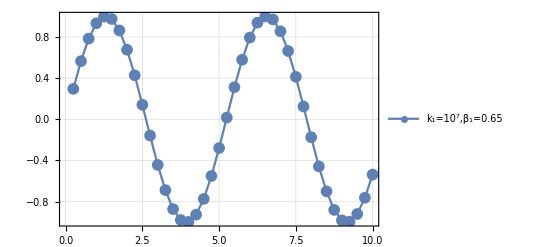

```mathematica
DiscretePlot[Subscript[uk107b0652, p],{p,0,10,Δt}, PlotLegends->{"k_1=10^7,β_1=0.65"},PlotTheme->"Detailed",Joined->True,PlotMarkers->{Automatic, 12},FillingStyle->White]
```

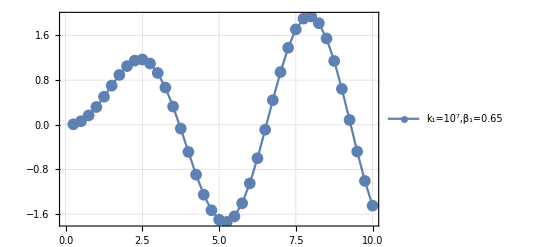

```mathematica
DiscretePlot[Subscript[uk107b0653, p],{p,0,10,Δt}, PlotLegends->{"k_1=10^7,β_1=0.65"},PlotTheme->"Detailed",Joined->True,PlotMarkers->{Automatic, 12},FillingStyle->White]
```

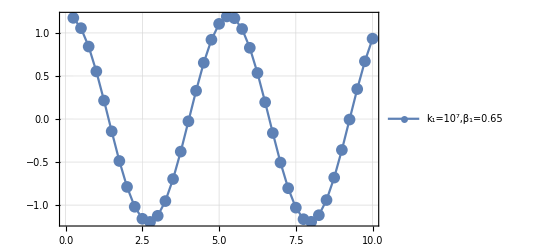

```mathematica
DiscretePlot[Subscript[uk107b065d2, p],{p,0,10,Δt}, PlotLegends->{"k_1=10^7,β_1=0.65"},PlotTheme->"Detailed",Joined->True,PlotMarkers->{Automatic, 12},FillingStyle->White]
```

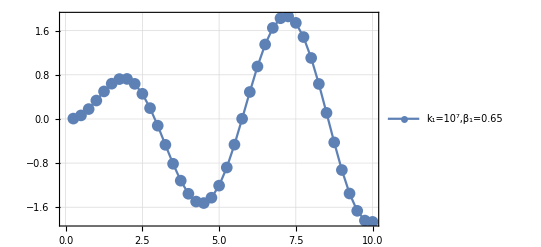

```mathematica
DiscretePlot[Subscript[uk107b065d3, p],{p,0,10,Δt}, PlotLegends->{"k_1=10^7,β_1=0.65"},PlotTheme->"Detailed",Joined->True,PlotMarkers->{Automatic, 12},FillingStyle->White]
```

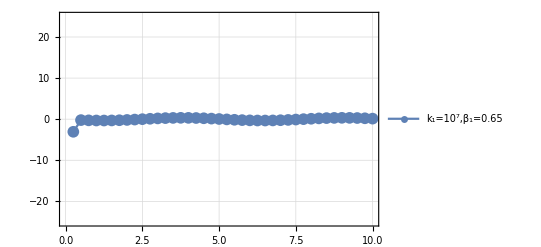

```mathematica
DiscretePlot[Subscript[uk107b065dd2, p],{p,0,10,Δt}, PlotLegends->{"k_1=10^7,β_1=0.65"},PlotTheme->"Detailed",Joined->True,PlotMarkers->{Automatic, 12},FillingStyle->White,PlotRange->25]
```

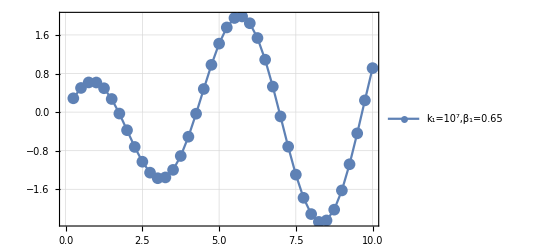

```mathematica
DiscretePlot[Subscript[uk107b065dd3, p],{p,0,10,Δt}, PlotLegends->{"k_1=10^7,β_1=0.65"},PlotTheme->"Detailed",Joined->True,PlotMarkers->{Automatic, 12},FillingStyle->White]
```